```mathematica
ClearAll[E1, E2, E3, z]
```

```mathematica
n1=1.500;
n2=1.500;
n3=1.500;
w1=30.0;
w2=30.0;
w3=w1+w2;
k1=n1 w1/c;
k2=n2 w2/c;
k3=n3 w3/c;
c=1;
X2=0.001;
Δk= k3-k2-k1
p1=2;
p1a=3;
p1a=4;
p2=6;
p2a=7;
p2b=8
xmax=10;
zmax=50;
equations={D[E3[x,z],z]==-I 1/(2 k3) D[E3[x,z], {x,2}]- I w3/(2 c n3) X2  E1[x,z]*E2[x,z] Exp[I Δk z],D[E2[x,z],z]==-I 1/(2 k2) D[E2[x,z], {x,2}]- I w2/(2 c n2) X2 E3[x,z]*Conjugate[E1[x,z]] Exp[-I Δk z], D[E1[x,z],z]==-I 1/(2 k1) D[E1[x,z], {x,2}]- I w1/(2 c n1) X2 E3[x,z]*Conjugate[E2[x,z]] Exp[-I Δk z]};

initials= {E1[x,0]==Exp[2 I Pi p1 x/xmax], E2[x,0]==Exp[2 I Pi p2 x/xmax],
E3[x,0]==0,
 E1[0,z]==E1[xmax,z],  E3[0,z]==E3[xmax,z], E2[0,z]==E2[xmax,z]};
initials2= {E1[x,0]==0.15 Exp[2 I Pi p1 x/xmax]+0.68Exp[2 I Pi p1a x/xmax]+0.15Exp[2 I Pi p1b x/xmax], E2[x,0]==0.15Exp[2 I Pi p2 x/xmax]+0.68Exp[2 I Pi p2a x/xmax]+0.15Exp[2 I Pi p2b x/xmax],
E3[x,0]==0,
 E1[0,z]==E1[xmax,z],  E3[0,z]==E3[xmax,z], E2[0,z]==E2[xmax,z]};
```

0.

8

```mathematica
s=NDSolve[{equations, initials2}, {E1, E2, E3}, {x, 0,xmax},{z,0,zmax}, MaxStepSize->0.08][[1]]
```

{E1→InterpolatingFunction[{{…, 0., 10., …}, {0., 50.}}, <>],E2→InterpolatingFunction[{{…, 0., 10., …}, {0., 50.}}, <>],E3→InterpolatingFunction[{{…, 0., 10., …}, {0., 50.}}, <>]}

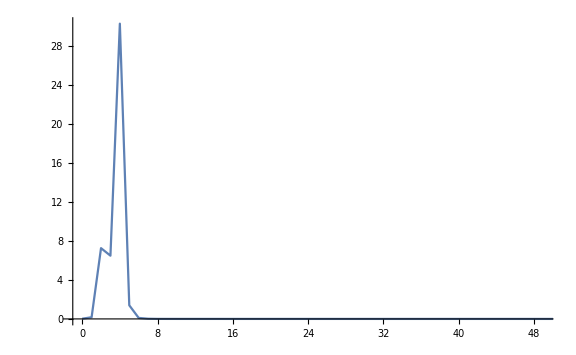

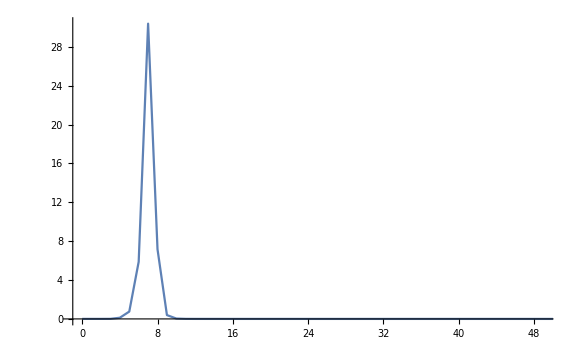

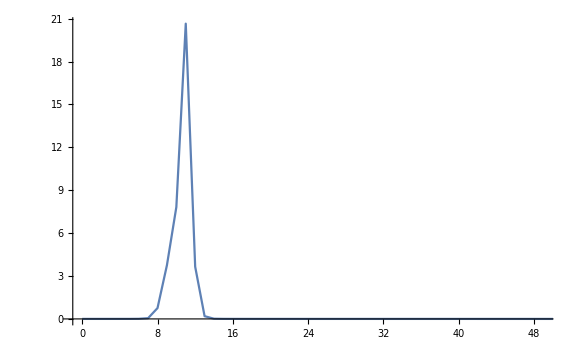

```mathematica
ListLinePlot[Abs[Fourier[Table[Re[E1[x,zmax]]/.s,{x,0,xmax,0.001}]]],PlotRange->{{0,50},All}, ImageSize->Large, Ticks->{Transpose[{Range[1,50,2],Range[0,49,2]}], Automatic}]
ListLinePlot[Abs[Fourier[Table[Im[E2[x,zmax]]/.s,{x,0,xmax,0.001}]]],PlotRange->{{0,50},All}, ImageSize->Large, Ticks->{Transpose[{Range[1,50,2],Range[0,49,2]}], Automatic}]
ListLinePlot[Abs[Fourier[Table[Re[E3[x,zmax]]/.s,{x,0,xmax,0.001}]]],PlotRange->{{0,50},All}, ImageSize->Large, Ticks->{Transpose[{Range[1,50,2],Range[0,49,2]}], Automatic}]
```

```mathematica
GraphicsGrid[{{Plot3D[Re[E1[x,z]]/.s, {x, 0,xmax},{z,0,zmax}, PlotRange->All, PlotPoints->25],Plot3D[Re[E2[x,z]]/.s, {x, 0,xmax},{z,0,zmax}, PlotRange->All]},{Plot3D[Abs[E3[x,z]]/.s, {x, 0,xmax},{z,0,zmax}, PlotRange->All,PlotPoints->25], Plot3D[(Abs[E1[x,z]]^2+Abs[E2[x,z]]^2+Abs[E3[x,z]]^2)/.s, {x, 0,xmax},{z,0,zmax}, PlotRange->All]}}, ImageSize->Full]
```

-Graphics-

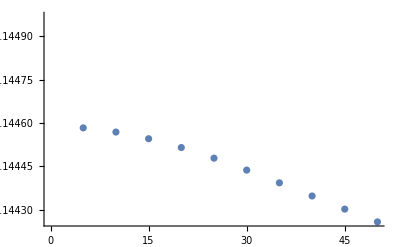

NIntegrate::ilim: Invalid integration variable or limit(s) in Null.

NIntegrate[Abs[E1[x,1]]^2+Abs[E2[x,1]]^2+Abs[E3[x,1]]^2/.s,Null,{x,0,xmax}]

0.104691-0.60844 ⅈ

$Aborted

```mathematica
ListPlot[Table[{l,NIntegrate[ ((Abs[E1[x,z]]^2+Abs[E2[x,z]]^2+Abs[E3[x,z]]^2)/.s)/.z->l,{x, 0,xmax}]}, {l,0,zmax,5}]]
NIntegrate[((Abs[E1[x,1]]^2+Abs[E2[x,1]]^2+Abs[E3[x,1]]^2)/.s), ,{x, 0, xmax}]
E1[2,3]/.s
Quiet[Plot[NIntegrate[ ((Abs[E1[x,z]]^2+Abs[E2[x,z]]^2+Abs[E3[x,z]]^2)/.s),{x, 0, xmax}], {z, 0, zmax}, PlotPoints->2]]
```